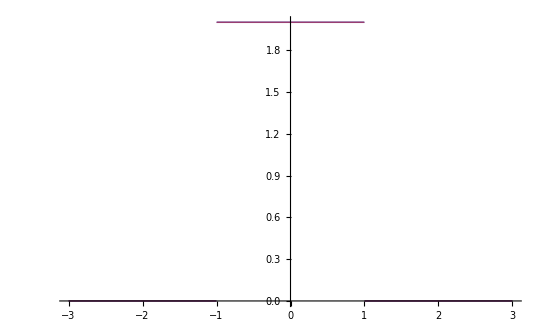

-Sign'[-1+x]+Sign'[1+x]

-2 DiracDelta[-1+Abs[x]] Abs'[x]

```mathematica
u[x_, a_]=Sign[x +a]-Sign[x-a];
u1[x_, a_]=2*HeavisideTheta[Abs[a]-Abs[x]]*Sign[a];
Plot[{u[x,1],u1[x,1]},{x,-3,3}]
du[x,a]=D[u[x,a],x]
du1[x,a]=D[u1[x,1],x]
```